```mathematica
f[x_]:=C[1] x^3 + C[2] x^2 +C[3] x + C[4]
g[x_]:=C[5] x^2 + C[6] x +C[7]
h[x_]:=C[8]Sin[C[9]x]+C[10]

D[f[x],x]
D[g[x],x]
D[h[x],x]

D[f[x],{x,2}]
D[g[x],{x,2}]
D[h[x],{x,2}]
```

3 x^2 C[1]+2 x C[2]+C[3]

2 x C[5]+C[6]

C[8] C[9] Cos[x C[9]]

6 x C[1]+2 C[2]

2 C[5]

-C[8] C[9]^2 Sin[x C[9]]

```mathematica
(* Ecuaciones de continuidad Aceleracion *)
Print["Segunda Derivada"]
D[g[x],{x,2}]==D[h[x],{x,2}]
D[g[x],{x,2}]==D[f[x],{x,2}]
D[f[x],{x,2}]==D[h[x],{x,2}]

(* Ecuaciones de continuidad Velocidad *)
Print["Primera Derivada"]
D[g[x],{x,1}]==D[h[x],{x,1}]
D[g[x],{x,1}]==D[f[x],{x,1}]
D[f[x],{x,1}]==D[h[x],{x,1}]

(* Posicion *)
Print["Funciones"]
g[x]==h[x]
g[x]==f[x]
f[x]==h[x]
```

Segunda Derivada

2 C[5]==-C[8] C[9]^2 Sin[x C[9]]

2 C[5]==6 x C[1]+2 C[2]

6 x C[1]+2 C[2]==-C[8] C[9]^2 Sin[x C[9]]

Primera Derivada

2 x C[5]+C[6]==C[8] C[9] Cos[x C[9]]

2 x C[5]+C[6]==3 x^2 C[1]+2 x C[2]+C[3]

3 x^2 C[1]+2 x C[2]+C[3]==C[8] C[9] Cos[x C[9]]

Funciones

x^2 C[5]+x C[6]+C[7]==C[10]+C[8] Sin[x C[9]]

x^2 C[5]+x C[6]+C[7]==x^3 C[1]+x^2 C[2]+x C[3]+C[4]

x^3 C[1]+x^2 C[2]+x C[3]+C[4]==C[10]+C[8] Sin[x C[9]]

```mathematica
ClearAll[f,g,h,l,α,β]
```

```mathematica
(* Vamos a poner restricciones *)
f[x_]:=C[1] x^3 + C[2] x^2 +C[3] x + C[4]
g[x_]:=C[5] x^2 + C[6] x +C[7]
h[x_]:=C[8]Sin[C[9]x]+C[10]

(* Cubica -> Cuadratica -> sinoidal *)
(* restric={x->α,C[4]->0,C[3]->0,C[5]->C[2],C[4]->C[7]}*)
restric1={x->α,C[2]->0,C[4]->0,C[9]->2Pi/l} (* Cubica -> Cuadratica *)

restric2={x->β,C[9]->2Pi/l} (* Cuadratica -> Sinoidal*)

eqn1=(f[x]==g[x])/.restric1
eqn2=(D[g[x],{x,2}]==D[f[x],{x,2}])/.restric1
eqn3=(D[g[x],{x,1}]==D[f[x],{x,1}])/.restric1

eqn4=(g[x]==h[x])/.restric2
eqn5=(D[g[x],{x,2}]==D[h[x],{x,2}])/.restric2
eqn6=(D[g[x],{x,1}]==D[h[x],{x,1}])/.restric2

sol1=Solve[{eqn1,eqn2,eqn3},{C[5],C[6],C[7]},Reals]
sol2=Solve[{eqn4,eqn5,eqn6},{C[5],C[6],C[7]},Reals]
```

{x→α,C[2]→0,C[4]→0,C[9]→(2 π)/l}

{x→β,C[9]→(2 π)/l}

α^3 C[1]+α C[3]==α^2 C[5]+α C[6]+C[7]

2 C[5]==6 α C[1]

2 α C[5]+C[6]==3 α^2 C[1]+C[3]

β^2 C[5]+β C[6]+C[7]==C[10]+C[8] Sin[(2 π β)/l]

2 C[5]==-(4 π^2 C[8] Sin[(2 π β)/l])/l^2

2 β C[5]+C[6]==(2 π C[8] Cos[(2 π β)/l])/l

{{C[5]→-(-α^3 C[1]-α C[3]+α (-3 α^2 C[1]+C[3])+1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3])))/α^2,C[6]→-3 α^2 C[1]+C[3],C[7]→1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3]))}}

{{C[5]→ConditionalExpression[-(2 π^2 C[8] Sin[(2 π β)/l])/l^2, l>0||l<0],C[6]→ConditionalExpression[(2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l)/l, l>0||l<0],C[7]→ConditionalExpression[C[10]+C[8] Sin[(2 π β)/l]+(2 π^2 β^2 C[8] Sin[(2 π β)/l])/l^2-(β (2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l))/l, l>0||l<0]}}

```mathematica
eqn7=-(-α^3 C[1]-α C[3]+α (-3 α^2 C[1]+C[3])+1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3])))/α^2==-(2 π^2 C[8] Sin[(2 π β)/l])/l^2
eqn8=-3 α^2 C[1]+C[3]==(2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l)/l
eqn9=1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3]))==C[10]+C[8] Sin[(2 π β)/l]+(2 π^2 β^2 C[8] Sin[(2 π β)/l])/l^2-(β (2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l))/l

Solve[{eqn8,eqn9},{C[1],C[3]},Reals]
```

-(-α^3 C[1]-α C[3]+α (-3 α^2 C[1]+C[3])+1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3])))/α^2==-(2 π^2 C[8] Sin[(2 π β)/l])/l^2

-3 α^2 C[1]+C[3]==(2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l)/l

1/2 (-α^3 C[1]+α C[3]-α (-3 α^2 C[1]+C[3]))==C[10]+C[8] Sin[(2 π β)/l]+(2 π^2 β^2 C[8] Sin[(2 π β)/l])/l^2-(β (2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l))/l

{{C[1]→(l^2 C[10]-2 l π β C[8] Cos[(2 π β)/l]+l^2 C[8] Sin[(2 π β)/l]-2 π^2 β^2 C[8] Sin[(2 π β)/l])/(l^2 α^3),C[3]→-1/l^2(-2 l π C[8] Cos[(2 π β)/l]-4 π^2 β C[8] Sin[(2 π β)/l]-(3 (l^2 C[10]-2 l π β C[8] Cos[(2 π β)/l]+l^2 C[8] Sin[(2 π β)/l]-2 π^2 β^2 C[8] Sin[(2 π β)/l]))/α)}}

```mathematica
(* Vamos a ver que onda *)

(* Restricciones *)
α= 5;(* Primera union *)
β= 15; (* Segunda union*)
l=4; (* Longitud de onda *)
m=1; (* Desplazamiento horizontal de la sinoidal *)
k=2;
b=0;
d=0;


i=0;



a=(l^2 C[10]-2 l π β C[8] Cos[(2 π β)/l]+l^2 C[8] Sin[(2 π β)/l]-2 π^2 β^2 C[8] Sin[(2 π β)/l])/(l^2 α^3);
c=-1/l^2(-2 l π C[8] Cos[(2 π β)/l]-4 π^2 β C[8] Sin[(2 π β)/l]-(3 (l^2 C[10]-2 l π β C[8] Cos[(2 π β)/l]+l^2 C[8] Sin[(2 π β)/l]-2 π^2 β^2 C[8] Sin[(2 π β)/l]))/α);
e=-(2 π^2 C[8] Sin[(2 π β)/l])/l^2;
i=(2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l)/l;
j=C[10]+C[8] Sin[(2 π β)/l]+(2 π^2 β^2 C[8] Sin[(2 π β)/l])/l^2-(β (2 π C[8] Cos[(2 π β)/l]+(4 π^2 β C[8] Sin[(2 π β)/l])/l))/l;

(*  Evaluacion de las funciones *)
f[x_]:=(C[1] x^3 + C[2] x^2 +C[3] x + C[4])/.{C[1]->a,C[2]->b,C[3]->c,C[4]->d}
g[x_]:=(C[5] x^2 + C[6] x +C[7])/.{C[5]->e,C[6]->i,C[7]->j}
h[x_]:=(C[8]Sin[C[9]x]+C[10])/.{C[8]->k,C[9]->l,C[10]->m}


f[x]/.eval
g[x]/.eval
h[x]/.eval
```

1/16 (-120 π^2+3/5 (-16+900 π^2)) x+((-16+900 π^2) x^3)/2000

-1+(225 π^2)/4-(15 π^2 x)/2+(π^2 x^2)/4

1+2 Sin[4 x]

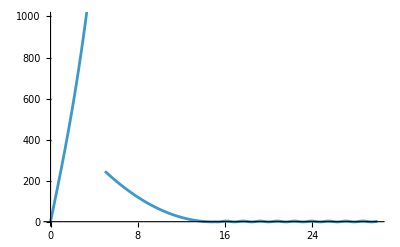

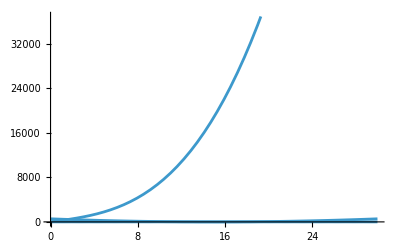

```mathematica
Show[List[
	Plot[{f[x]}/.eval,{x,0,α}],
	Plot[{g[x]}/.eval,{x,α,β}],
	Plot[{h[x]}/.eval,{x,β,2β}]
],PlotRange->{{0,2β},{-1,1000}}]
```

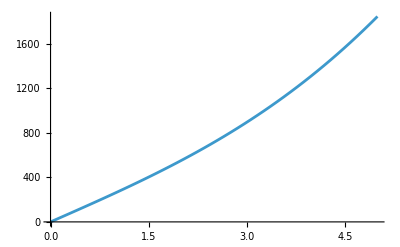
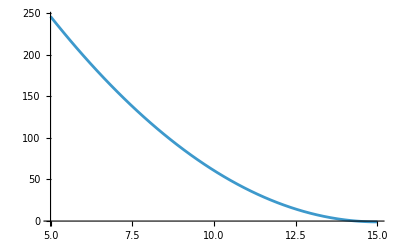
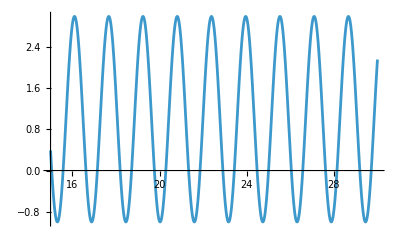

```mathematica
List[
	Plot[{f[x]}/.eval,{x,0,α}],
	Plot[{g[x]}/.eval,{x,α,β}],
	Plot[{h[x]}/.eval,{x,β,2β}]
]
```

```mathematica
(* Vamos a poner restricciones *)
f[x]
g[x]
h[x]

(* Sinoidal -> Cuadratica -> cubica *)
(* restric={x->α,C[4]->0,C[3]->0,C[5]->C[2],C[4]->C[7]}*)
restric1={x->α,C[9]->2Pi/l} (* Sinoidal -> Cuadratica *)

eqn1=(h[x]==g[x])/.restric1
eqn2=(D[h[x],{x,2}]==D[g[x],{x,2}])/.restric1
eqn3=(D[h[x],{x,1}]==D[g[x],{x,1}])/.restric1

sol1=Solve[{eqn1,eqn2,eqn3},{C[5],C[6],C[7]},Reals]
```

x^3 C[1]+x^2 C[2]+x C[3]+C[4]

x^2 C[5]+x C[6]+C[7]

C[10]+C[8] Sin[x C[9]]

{x→α,C[9]→(2 π)/l}

C[10]+C[8] Sin[(2 π α)/l]==α^2 C[5]+α C[6]+C[7]

-(4 π^2 C[8] Sin[(2 π α)/l])/l^2==2 C[5]

(2 π C[8] Cos[(2 π α)/l])/l==2 α C[5]+C[6]

{{C[5]→ConditionalExpression[-(2 π^2 C[8] Sin[(2 π α)/l])/l^2, l>0||l<0],C[6]→ConditionalExpression[-(-2 π C[8] Cos[(2 π α)/l]-(4 π^2 α C[8] Sin[(2 π α)/l])/l)/l, l>0||l<0],C[7]→ConditionalExpression[C[10]+C[8] Sin[(2 π α)/l]+(2 π^2 α^2 C[8] Sin[(2 π α)/l])/l^2+(α (-2 π C[8] Cos[(2 π α)/l]-(4 π^2 α C[8] Sin[(2 π α)/l])/l))/l, l>0||l<0]}}